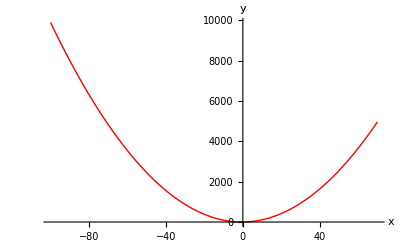

```mathematica
Plot[1 + x + x^2, {x, -100, 70}, 
PlotStyle->{Red, Thick},
AxesLabel->{"x" ,"y"},
PlotRange->All,
Ticks->Automatic,
PlotPoints->100]
```

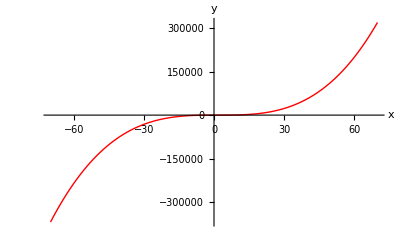

```mathematica
Plot[(x-1)(x-2)^2 , {x, -70, 70}, 
PlotStyle->{Red, Thick},
AxesLabel->{"x" ,"y"},
PlotRange->All,
Ticks->Automatic,
PlotPoints->100]
```

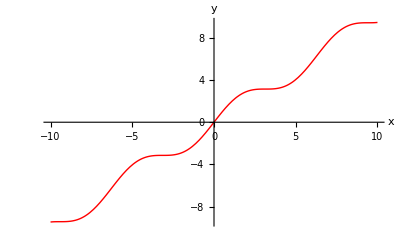

```mathematica
Plot[x+ Sin[x], {x, -10, 10}, 
PlotStyle->{Red, Thick},
AxesLabel->{"x" ,"y"},
PlotRange->All,
Ticks->Automatic,
PlotPoints->100]
```

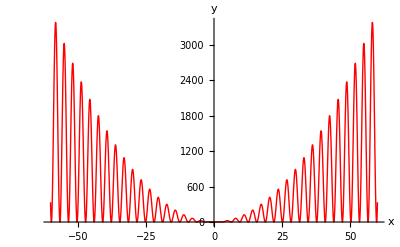

```mathematica
Plot[x^2 Sin[x]^2, {x, -60, 60}, 
PlotStyle->{Red, Thick},
AxesLabel->{"x" ,"y"},
PlotRange->All,
Ticks->Automatic,
PlotPoints->100]
```

```mathematica
y[x_] := (x^2(x-1))/(x+1)^2;
D[y[x],x]
```

-(2 (-1+x) x^2)/(1+x)^3+(2 (-1+x) x)/(1+x)^2+x^2/(1+x)^2

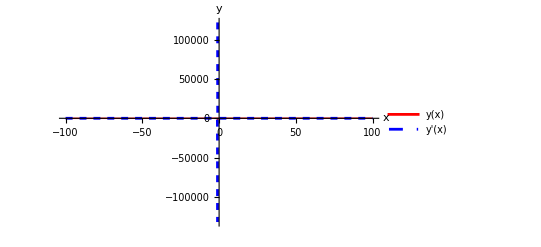

```mathematica
Plot[{(x^2(x-1))/(x+1)^2,-(2 (-1+x) x^2)/(1+x)^3+(2 (-1+x) x)/(1+x)^2+x^2/(1+x)^2},{x,-100,100},PlotStyle->{{Red,Thick},{Blue,Dashed}},(*设置曲线颜色和样式*)AxesLabel->{"x","y"},(*设置坐标轴标记*)PlotLegends->{"y(x)","y'(x)"},(*图例标注 y(x) 和 y'(x)*)PlotRange->All,(*自动调整 y 轴范围*)Ticks->Automatic,(*自动生成坐标刻度*)PlotPoints->100           (*设置计算点数*)]
```

```mathematica
y[x_]:=Sin[x]/(1+x^2);
D[y[x],x]
```

Cos[x]/(1+x^2)-(2 x Sin[x])/((1+x^2)^2)

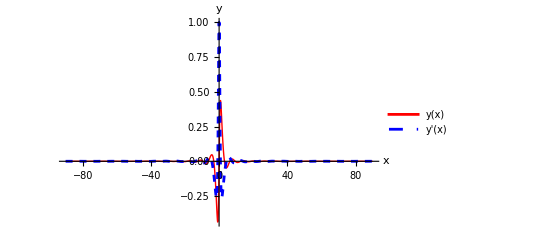

```mathematica
Plot[{Sin[x]/(1+x^2),Cos[x]/(1+x^2)-(2 x Sin[x])/((1+x^2)^2)},{x,-90,90},PlotStyle->{{Red,Thick},{Blue,Dashed}},(*设置曲线颜色和样式*)AxesLabel->{"x","y"},(*设置坐标轴标记*)PlotLegends->{"y(x)","y'(x)"},(*图例标注 y(x) 和 y'(x)*)PlotRange->All,(*自动调整 y 轴范围*)Ticks->Automatic,(*自动生成坐标刻度*)PlotPoints->100           (*设置计算点数*)]
```

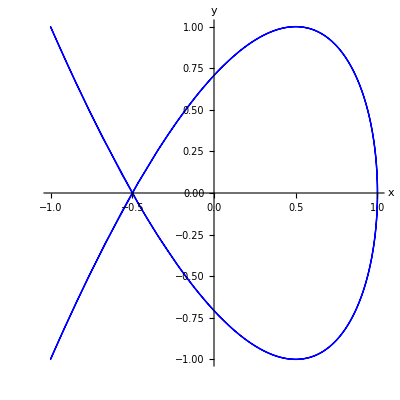

```mathematica
ParametricPlot[{Cos[2 t],Sin[3 t]},{t,0,2 Pi},PlotStyle->{Thick,Blue},(*设置曲线样式*)AxesLabel->{"x","y"},(*设置坐标轴标记*)Ticks->Automatic,(*自动生成刻度*)PlotRange->All,(*自动调整坐标范围*)AspectRatio->1             (*保持 x 和 y 的比例相同*)]
(*Set a =  1*)
```

```mathematica
Plot3D[(x^2-y^2)/(x^3+y^3),{x,-10,10},{y,-10,10},PlotStyle->Directive[Orange,Opacity[0.8]],(*设置颜色和透明度*)Mesh->None,(*取消网格线*)AxesLabel->{"x","y","z"},(*设置坐标轴标记*)PlotRange->All,(*自动调整 z 轴范围*)Boxed->True (*显示坐标轴盒*)]
```

-Graphics3D-

```mathematica
Plot3D[1/(y^2-x^3+3 x -3),{x,-3,3},{y,-3,3},PlotStyle->Directive[Orange,Opacity[0.8]],(*设置颜色和透明度*)Mesh->None,(*取消网格线*)AxesLabel->{"x","y","z"},(*设置坐标轴标记*)PlotRange->All,(*自动调整 z 轴范围*)Boxed->True, 
(*显示坐标轴盒*)
RegionFunction->Function[{x,y,z},0<Mod[x^2+y^2,2]<1]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u *Sin[t],u*Cos[t],t/3},{u,-1,1},{t,0,15},PlotStyle->Directive[Blue,Opacity[0.7]],(*设置颜色和透明度*)Mesh->None,(*去掉网格线*)AxesLabel->{"x","y","z"},(*设置坐标轴标记*)Boxed->True,(*显示坐标轴盒*)PlotRange->All (*自动调整 z 轴范围*)]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,Sqrt[1-x^2-y^2]},{x,-1,1},{y,-1,1},PlotStyle->Directive[Blue,Opacity[0.7]],(*设置颜色和透明度*)Mesh->None,(*去掉网格线*)AxesLabel->{"x","y","z"},(*设置坐标轴标记*)Boxed->True,(*显示坐标轴盒*)PlotRange->All (*自动调整 z 轴范围*)]
```

-Graphics3D-